# Persymmetric 3 × 3 matrices

## Characteristic polynomials, nilpotency, and prescribed patterns

All parameters are real unless stated otherwise. The input cells are evaluated sequentially, using exact arithmetic throughout.

## 1. The general persymmetric matrix

Let J denote the reversal matrix of order 3. Since J = Jᵀ = J⁻.b9, the persymmetry condition A = JAᵀJ is equivalent to the symmetry of JA. The general form below has six independent real parameters; the anti-diagonal entries d, e and f are unconstrained by the reflection.

```mathematica
ClearAll["Global`*"]; j3 = Reverse[IdentityMatrix[3]]; a3 = {{a, b, d}, {c, e, b}, {f, c, a}}; {MatrixForm[j3], MatrixForm[a3]}
```

{(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0),(a | b | d
c | e | b
f | c | a)}

```mathematica
{Simplify[a3 == j3.Transpose[a3].j3], Simplify[j3.a3 == Transpose[j3.a3]]}
```

{True,True}

The two identities verify persymmetry and its equivalent formulation through JA. Thus the real persymmetric matrices of order 3 form a six-dimensional linear subspace.

## 2. Characteristic polynomial

Set χ(x) = det(xI - A). Mathematica's CharacteristicPolynomial[A, x] uses det(A - xI), so its output is -χ(x) in dimension 3. The final equality below checks this sign convention.

```mathematica
chi = Expand[Det[x IdentityMatrix[3] - a3]]; chi
```

2 a b c-c^2 d-a^2 e-b^2 f+d e f+a^2 x-2 b c x+2 a e x-d f x-2 a x^2-e x^2+x^3

```mathematica
detA = Factor[Det[a3]]; expected = x^3 - (2 a + e) x^2 + (a^2 + 2 a e - 2 b c - d f) x - detA; {detA, FullSimplify[chi == expected], FullSimplify[chi == -CharacteristicPolynomial[a3, x]]}
```

{-2 a b c+c^2 d+a^2 e+b^2 f-d e f,True,True}

Collecting coefficients gives

χ(x) = x.b3 - (2a + e)x.b2 + (a.b2 + 2ae - 2bc - df)x - det(A),

det(A) = a.b2e - 2abc + b.b2f + c.b2d - def.

Here 2a + e is the trace, while a.b2 + 2ae - 2bc - df is the sum of the principal minors of order 2. The symbolic checks confirm the expansion and the overall sign.

## 3. Characterisation of χ(x) = x.b3

Equating the constant, linear and quadratic coefficients to zero gives the following system. Eliminating e through the trace condition yields e = -2a.

```mathematica
coefficientEquations = Table[Coefficient[chi, x, k] == 0, {k, 0, 2}]; coefficientEquations // TableForm
```

2 a b c-c^2 d-a^2 e-b^2 f+d e f==0
a^2-2 b c+2 a e-d f==0
-2 a-e==0

```mathematica
traceRule = e -> -2 a; reducedPolynomial = Expand[chi /. traceRule]; reducedPolynomial
```

2 a^3+2 a b c-c^2 d-b^2 f-2 a d f-3 a^2 x-2 b c x-d f x+x^3

```mathematica
nilpotentConditions = {e == -2 a, 3 a^2 + 2 b c + d f == 0, -2 a^3 - 2 a b c + b^2 f + c^2 d + 2 a d f == 0}; nilpotentConditions // TableForm
```

e==-2 a
3 a^2+2 b c+d f==0
-2 a^3-2 a b c+c^2 d+b^2 f+2 a d f==0

These three equations are necessary and sufficient for χ(x) = x.b3. By Cayley–Hamilton they imply A.b3 = 0; conversely, A.b3 = 0 forces all eigenvalues to vanish. The trace condition alone is insufficient.

For constructing examples, substitution of df = -3a.b2 - 2bc into the determinant condition gives the equivalent system

e = -2a,     df = -3a.b2 - 2bc,     b.b2f + c.b2d = 8a.b3 + 6abc.

## 4. A nonnegative example

The upper shift U provides a nonnegative persymmetric realisation of the spectrum {0, 0, 0}. The output records U, the persymmetry check, its characteristic polynomial, U.b2 and U.b3.

```mathematica
upperShift = {{0, 1, 0}, {0, 0, 1}, {0, 0, 0}}; {MatrixForm[upperShift], Simplify[upperShift == j3.Transpose[upperShift].j3], Expand[Det[x IdentityMatrix[3] - upperShift]], MatrixForm[MatrixPower[upperShift, 2]], MatrixForm[MatrixPower[upperShift, 3]]}
```

{(0 | 1 | 0
0 | 0 | 1
0 | 0 | 0),True,x^3,(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

Upper triangularity gives χ(x) = x.b3. Since U.b2 has a nonzero (1,3) entry and U.b3 = 0, its minimal polynomial is x.b3 and its nilpotency index is 3.

## 5. Signed cycles can cancel

Consider the signed persymmetric matrix M below. The output verifies χ(x) = x.b3, M.b2 ≠ 0 and M.b3 = 0, so M has nilpotency index 3 despite the directed cycles in its nonzero pattern.

```mathematica
mixedCycles = {{0, 1, 1}, {2, 0, 1}, {-4, 2, 0}}; {MatrixForm[mixedCycles], Simplify[mixedCycles == j3.Transpose[mixedCycles].j3], Expand[Det[x IdentityMatrix[3] - mixedCycles]], MatrixForm[MatrixPower[mixedCycles, 2]], MatrixForm[MatrixPower[mixedCycles, 3]]}
```

{(0 | 1 | 1
2 | 0 | 1
-4 | 2 | 0),True,x^3,(-2 | 2 | 1
-4 | 4 | 2
4 | -4 | -2),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

### Cancellation in the characteristic coefficients

For the general zero-diagonal persymmetric matrix, the expression in section 2 reduces to

χ(x) = x.b3 - (2bc + df)x - (b.b2f + c.b2d).

For M, the products associated with the three directed 2-cycles and the two directed 3-cycles satisfy

2bc + df = (1 × 2) + (1 × 2) + (1 × (-4)) = 0,

b.b2f + c.b2d = (1 × 1 × (-4)) + (1 × 2 × 2) = 0.

Together with the zero trace, these cancellations account for every coefficient below x.b3. The sign pattern displayed next is realised by a nilpotent matrix, but does not force nilpotency for every choice of magnitudes.

```mathematica
signPattern = Map[Which[# > 0, "+", # < 0, "-", True, "0"] &, mixedCycles, {2}]; Grid[signPattern, Frame -> All]
```

0 | + | +
+ | 0 | +
- | + | 0

For example, replacing the (3,1) entry -4 by -3 preserves both persymmetry and the sign pattern, but changes the characteristic polynomial to x.b3 - x - 1.

### The directed nonzero pattern

For any square matrix B, define G(B) on the matrix indices by i → j exactly when the (i,j) entry is nonzero, including loops for nonzero diagonal entries. The following graph records this pattern for M; it does not encode edge signs or magnitudes.

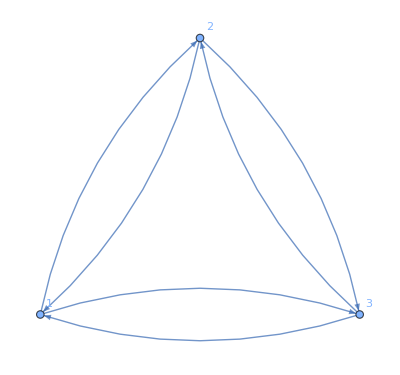

```mathematica
adjacency = Map[Boole[# != 0] &, mixedCycles, {2}]; AdjacencyGraph[adjacency, DirectedEdges -> True, VertexLabels -> "Name"]
```

The link with matrix powers is the weighted-walk identity. For a directed walk w = (i₀, …, iₖ), let wt(w) be the product of the matrix entries corresponding to its successive edges. Then

(B^k)_ij=∑_(w:i→j,|w|=k) wt(w)

Here k ≥ 1 and |w| denotes the number of edges, with repetitions permitted. This is the usual matrix-product expansion, organised by walks in G(B).

In M, the length-three closed walks based at vertex 1 are 1 → 2 → 3 → 1 and 1 → 3 → 2 → 1, with weights -4 and +4. Thus the (1,1) entry of M.b3 is zero. The full matrix computation above verifies cancellation in every entry of the cube.

### Consequences for prescribed patterns

Acyclic pattern. If G(B) is acyclic on n vertices, it has no walk of length n. The weighted-walk identity therefore gives Bⁿ = 0, independently of the signs of the nonzero entries. In particular, G(U) is the chain 1 → 2 → 3.

Nonnegative case. If B is entrywise nonnegative and G(B) contains a directed cycle of length l and weight c > 0 through i, repeating that cycle gives the bound below for every positive integer r.

(B^rl)_ii≥c^r>0

Hence B has nonzero powers of arbitrarily large order and cannot be nilpotent. Together with the acyclic case, this proves that an entrywise nonnegative matrix is nilpotent if and only if its directed nonzero pattern is acyclic.

Signed case. Negative walk weights invalidate the positivity argument. The matrix M exhibits this obstruction: its graph identifies the available cycle products, while their values determine cancellation. Thus the graph supplies structural restrictions on a prescribed pattern, rather than a nilpotency test for arbitrary signed matrices.

## 6. Nonzero diagonal and a smaller nilpotency index

The next example N has a = 1 and e = -2. It demonstrates that a signed persymmetric nilpotent matrix may have nonzero diagonal entries and nilpotency index 2.

```mathematica
rankOneExample = {{1, 1, -1/2}, {-2, -2, 1}, {-2, -2, 1}}; {MatrixForm[rankOneExample], Simplify[rankOneExample == j3.Transpose[rankOneExample].j3], Expand[Det[x IdentityMatrix[3] - rankOneExample]], MatrixRank[rankOneExample], MatrixForm[MatrixPower[rankOneExample, 2]]}
```

{(1 | 1 | -1/2
-2 | -2 | 1
-2 | -2 | 1),True,x^3,1,(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

The rank-one structure explains the vanishing square: N = uvᵀ with u = (1, -2, -2)ᵀ and v = (1, 1, -1/2)ᵀ. Since vᵀu = 0, we have N.b2 = u(vᵀu)vᵀ = 0. As N ≠ 0, its minimal polynomial is x.b2, although its characteristic polynomial remains x.b3.

## 7. Reality of eigenvalues is not automatic

The following matrix is both persymmetric and real skew-symmetric. Its characteristic polynomial x(x.b2 + 2) gives the spectrum {0, i√2, -i√2}, demonstrating that real persymmetry alone does not imply a real spectrum.

```mathematica
complexExample = {{0, 1, 0}, {-1, 0, 1}, {0, -1, 0}}; {Simplify[complexExample == j3.Transpose[complexExample].j3], Factor[Det[x IdentityMatrix[3] - complexExample]], Eigenvalues[complexExample]}
```

{True,x (2+x^2),{ⅈ √2,-ⅈ √2,0}}

## 8. Nonnegative specialization

Suppose A is entrywise nonnegative and χ(x) = x.b3. The trace condition gives a = e = 0. The remaining equations are 2bc + df = 0 and b.b2f + c.b2d = 0; nonnegativity therefore yields

a = e = 0,     bc = df = 0,     b.b2f = c.b2d = 0.

Conversely, these equalities force χ(x) = x.b3. They eliminate loops, directed 2-cycles and directed 3-cycles, respectively, giving the entrywise version of the acyclicity criterion in this dimension. For signed entries, the coefficient equations instead permit cancellation between the corresponding products.